```mathematica
BB ={{-3420, 27.3},
{-2920, 22.4},
{-2420, 18.1},
{-1920, 17.0},
{-1420, 15.3},
{-920, 14.6},
{-420, 14.2},
{80, 14.6},
{580, 15.3},
{1080, 16.5},
{1580, 17.8},
{3080, 32.3},
{2580, 24.0},
{2080, 20.6},
{-3670, 32.3},
{-3170, 23.8},
{-2670, 21},
{2746, 25.7},
{2913, 29.2}}
```

{{-3420,27.3},{-2920,22.4},{-2420,18.1},{-1920,17.},{-1420,15.3},{-920,14.6},{-420,14.2},{80,14.6},{580,15.3},{1080,16.5},{1580,17.8},{3080,32.3},{2580,24.},{2080,20.6},{-3670,32.3},{-3170,23.8},{-2670,21},{2746,25.7},{2913,29.2}}

```mathematica
{{-3420,27.3},{-2920,22.4},{-2420,18.1},{-1920,17.},{-1420,15.3},{-920,14.6},{-420,14.2},{80,14.6},{580,15.3},{1080,16.5},{1580,17.8}}
```

```mathematica
2580+2(500/3) //N
```

2913.33

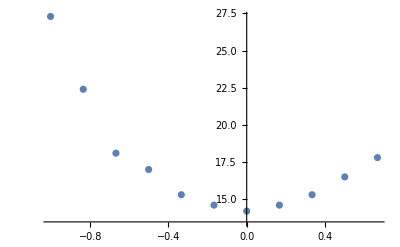

```mathematica
plot1 = BB // Map[{π(#[[1]]+420)/9400,#[[2]]}&]//N //ListPlot
```

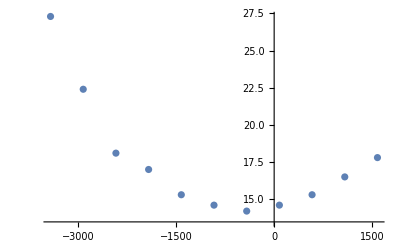

```mathematica
ListPlot[BB]
```

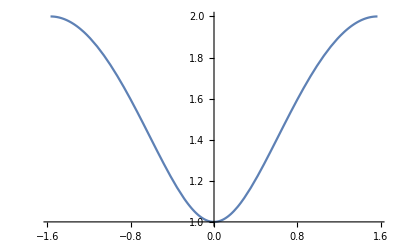

```mathematica
plot2 = Plot[√(g1^2 Cos[θ]^2 +g2^2 Sin[θ]^2)/. {g1 -> 1, g2 -> 2} , {θ, -π/2, π/2}]
```

```mathematica
360*(180/6.95)
```

9323.74

```mathematica
Manipulate[{
BB // Map[{π(#[[1]]+420)/9323,#[[2]]}&]//N //ListPlot,
Plot[12/g1 1.2 √(g1^2 Cos[θ]^2 +g2^2 Sin[θ]^2) , {θ, -π/2, π/2}]
}// Show[#,
PlotRange->All,
PlotLabel->{g1,g2}
]& ,
{ {g1,1},0.5,2},
{ {g2,2},0.5,5}
]
```

```mathematica
ff=-t Log[ 2 Cosh[ (g b)/t]]
```

-t Log[2 Cosh[(b g)/t]]

```mathematica
s=D[ff,t]
```

-Log[2 Cosh[(b g)/t]]+(b g Tanh[(b g)/t])/t

```mathematica
c = t D[s,t]//FullSimplify
```

-(b^2 g^2 Sech[(b g)/t]^2)/t^2

```mathematica
c/t/.{t->1,g->1}
```

-b^2 Sech[b]^2

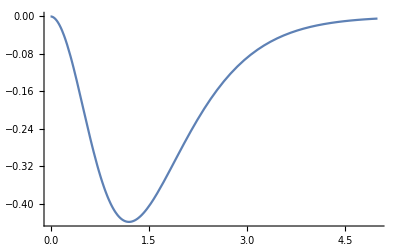

```mathematica
Plot[ c/t/.{t->1,g->1},{b,0,5}, PlotRange->All]
```

```mathematica
-3920 LinguisticAssistant
```

```mathematica
-3920 + 250
```

-3670

```mathematica
Manipulate[{
BB // Map[{π(#[[1]]+420)/9323,1/(#[[2]])}&]//N //ListPlot,
Plot[1/(12/g1 1.2 √(g1^2 Cos[θ]^2 +g2^2 Sin[θ]^2)) , {θ, -π/2, π/2}]
}// Show[#,
PlotRange->All,
PlotLabel->{g1,g2}
]& ,
{ {g1,1},0.5,2},
{ {g2,2},0.5,5}
]
```

```mathematica
Manipulate[{
BB // Map[{π(#[[1]]+420)/9323,1/(#[[2]])}&]//N //ListPlot,
Plot[1/(12 1.2 √(Cos[θ]^2 +r^2 Sin[θ]^2)) , {θ, -π/2, π/2}]
}// Show[#,
PlotRange->All,
PlotLabel->{g1,g2}
]& ,
{ {r,1},0.1,10}
]
```

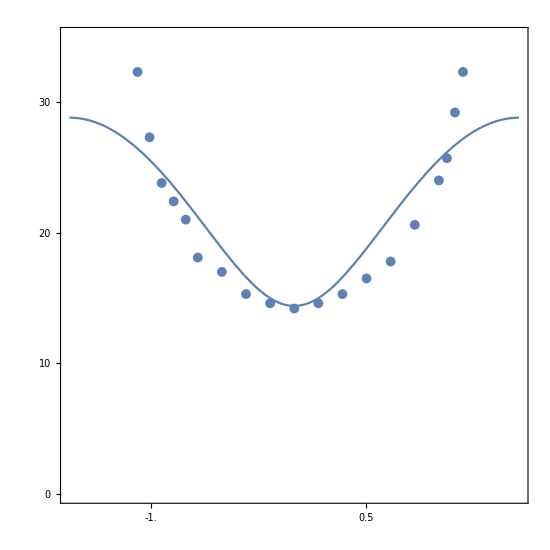

```mathematica
graph1 = Module[ {g1, g2},
g1 =1;
g2 = 2;
{
BB // Map[{π(#[[1]]+420)/9323,#[[2]]}&]//N //ListPlot,
Plot[12/g1 1.2 √(g1^2 Cos[θ]^2 +g2^2 Sin[θ]^2) , {θ, -π/2, π/2}]
}//nice// Show[#,
PlotRange->{ {-π/2,π/2},{0,35} },
Frame -> True,
AspectRatio -> 1,
FrameTicks->{
ticksstd[#&, 25][0,100,10],
ticksstd[#&, 25][-4,4,0.5]
}


]&
]
```

```mathematica
aaa=ListPlot[#,
PlotMarkers->{Automatic, 12},
PlotStyle->{Red}]&
```

ListPlot[#1,PlotMarkers→{Automatic,12},PlotStyle→{Red}]&

```mathematica
{ {1,2},{3,4}}//ListPlot[#,
PlotMarkers->{Automatic, 12},
PlotStyle->{Red}]&
```

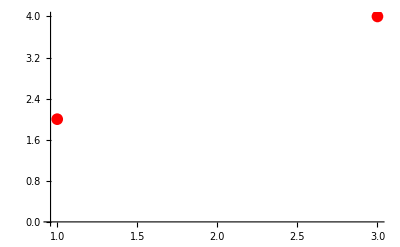

```mathematica
ListPlot[{ {1,2},{3,4}},
PlotMarkers->{Automatic, 12},
PlotStyle->{Red}]
```

```mathematica
aaa[{ {1,2},{3,4}}]
```

-Graphics-

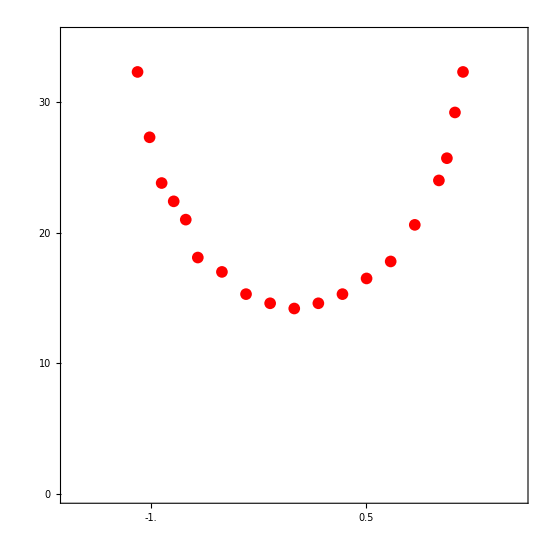

```mathematica
graph1 = Module[ {g1, g2},
g1 =1;
g2 = 2;
{
BB // Map[{π(#[[1]]+420)/9323,#[[2]]}&]//N //ListPlot[#,
PlotMarkers->{Automatic, 12},
PlotStyle->{Red}]&

}//nice// Show[#,
PlotRange->{ {-π/2,π/2},{0,35} },
Frame -> True,
AspectRatio -> 1,
FrameTicks->{
ticksstd[#&, 25][0,100,10],
ticksstd[#&, 25][-4,4,0.5]
}


]&
]
```

```mathematica
NotebookDirectory[]
```

D:\data\nanocal-Mar2020\

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\data\nanocal-Mar2020

```mathematica
Export["graph1-nice.pdf",graph1]
```

graph1-nice.pdf